```mathematica
Exit[];
```

```mathematica
f[y_]:={-Sin[y[[2]]-b]*F/d,y[[1]],y[[4]],F*er[b]+d*y[[1]]^2*er[y[[2]]]+Sin[y[[2]]-b]*F*ea[y[[2]]]}
```

```mathematica
er[alpha_]:={Cos[alpha],Sin[alpha]};ea[alpha_]:={-Sin[alpha],Cos[alpha]};
```

```mathematica
Pos[y_]:=y[[3]]+d*er[y[[2]]];
```

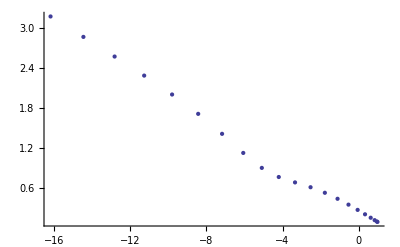

```mathematica
n=3;h=0.1;d=1;b=Pi/180*(-190);F=1;y={0,0.1,{0,0},{0,0}};

P=Table[0,{21}];P[[1]]=Pos[y];
For[i=0,i<20*n,i++,

y+=h*f[y];
P[[Floor[i/n]+2]]=Pos[y];
];
ListPlot[P,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
P
```

{{0.544801,0.841469},{0.559293,0.841457},{0.58377,0.841422},{0.618222,0.841356},{0.66264,0.841249},{0.717014,0.841097},{0.781331,0.840898},{0.855579,0.840653},{0.939749,0.840368},{1.03383,0.840055},{1.13782,0.839729},{1.2517,0.839406},{1.3755,0.839109},{1.50921,0.838855},{1.65285,0.838666},{1.80645,0.838554},{1.97002,0.838528},{2.1436,0.838593},{2.32721,0.838742},{2.52087,0.838965}}